```mathematica
SetDirectory[NotebookDirectory[]];
Remove["Global`*"]//Quiet;
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"lib_v_3.nb"}],InsertResults->False];
```

# Teoria gier

## Notacja

Wypłata. W pierwszej kolejności jest prowadzna notacja oraz częściowo przypomniana notacja. Wypłata gracza i∈ℐ w profilu strategii s∈S jest dana wzorem

u_i(s)=∑_(a∈A) p(s,a)·u_i(a),

gdzie p(s,a) to prawdopodobieństwo wystąpienia profilu akcji a∈A jeżeli grany jest profil strategii s. Jak określony jest już profil akcji a to z definicji określona jest wypłata graczy a więc w szczególności gracza i-tego. Podobnie można oznaczyć p(s_-i,a_-i) jeżeli chcemy mieć prawdopodobieństwo, że zdarzy się profil akcji a_-i przy profilu strategii s_-i gdzie w obu profilach został pominięty gracz i∈ℐ.

Dodatkowe proste funkcje. Jeżeli dany jest profil strategii s, w którym dla gracza i∈ℐ zamienimy jego strategię s_i na akcję j-tą, oznaczaną przez a_ij∈A_i, to jego wypłata będzie oznaczana przez

x_ij(s)=u_i(a_ij,s_-i)=∑_(a_-i∈A_-i) p(s_-i,a_-i)·u_i(a_ij,a_-i).

Następnie definiujemy funkcję

z_ij(s)=x_ij(s)-u_i(s).

Jest to różnica, dla gracza i∈ℐ, pomiędzy graniem w profilu s, j-tej akcji zamiast strategii s_i. Warto zauważyć, że jeżeli profil strategii s jest równowagą Nasha, a akcja a_ij należy do nośnika tej równowagi Nasha, to zachodzi z_ij(s)=0. Jeżeli profil s jest równowagą Nasha a akcja a_ij nie należy do jej nośnika to zawsze musi zachodzić z_ij(s)≤0, gdzie 0 może zachodzić jeżeli dwie akcje dają te same wypłaty (ale np. nie w przypadku strict Nasha equilibria, które są zawsze w akcjach). Jeżeli istnieje jakiś gracz i oraz jakaś jego akcja a_ij, dla której z_ij(s)>0 to profil s nie jest równowagą Nasha.

Ostatecznie definiujemy funkcję

g_ij(s)=max{z_ij(s),0}.

Jedyna różnica w stosunku do funkcji z_ij(s) jest taka, że ta funkcja nie może przyjmować wartości ujemnych.

## Charakteryzacja równowagi Nasha jako zbioru semialgebraicznego

### Charakteryzacja

Przede wszystkim, z samej definicji odwzorowania z wynika, że jeżeli profil s jest równowagą Nasha to z(s)≤0. Z drugiej strony, jeżeli dla jakiegoś profilu s zachodzi z(s)≤0 to profil ten musi być równowagą Nasha bo jeżeli z(s)≤0 to dla dowolnego gracza i oraz dla dowolnej akcji j zachodzi

z_ij(s)≤0
x_ij(s)-u_i(s)≤0
x_ij(s)≤u_i(s)
u_i(a_ij,s_-i)≤u_i(s)

Konsekwentnie dowolna akcja dowolnego gracza nie może mu dać więcej niż jego wypłata w profilu s a wiec nie ma żadnych zachęt do zmiany. Konsekwentnie profil s jest równowagą Nasha.

Fakt. Zbiór równowag Nasha, to zbiór punktów s∈S spełniających układ nierówności z(s)≤0.

Uwaga. Aby dobrze opisać kolejną metodę należy wprowadzić pewne obiekty z zakresu geometrii algebraicznej.

Definicja. (Basic algebraic function). Podstawową funkcją algebraiczną zadaną przez wielomian f(x_1,…,x_n,y) i liczbę naturalną k jest funkcja postaci

root_(y,k)f:ℝ^n∋x_1,…,x_n→root_(y,k)f(x_1,…,x_n)∈ℝ,

gdzie root_(y,k)f(x_1,…,x_n) jest k-tym pierwiastkiem rzeczywistym wielomianu f(x_1,…,x_n,y) traktowanego jako wielomian zmiennej y∈ℝ.

Definicja. (Real algebraic function). Rzeczywistą funkcją algebraiczną jest dowolne złożenie wielomianu, podstawowej funkcji algebraicznej oraz funkcji wykładniczych z wymiernymi potęgami.

Definicja. (System of real algebraic equations and inequalities). Układem rzeczywistych równań i nierówności algebraicznych w zmiennych x_1,…,x_n jest suma koniungcji wyrażeń

f_k(x_1,…,x_n)ρ_k g_k(x_1,…,x_n),

gdzie ρ_k∈{<,≤,≥,>,=,≠} i f_k,g_k są rzeczywistymi funkcjami algebraicznymi.

Przykład. Niech dany będzie układ postaci

x≥0∧√x<1∨x<0∧√-x<1.

Układ ten jest niewątpliwie układem nierówności algebraicznych. Jego rozwiązaniem jest zbiór -1<x<1. Warto zauważyć, że 0 należy tylko do dziedziny jednego z elementów alternatywy.

Definicja. (Quantified system of real algebraic equations and inequalities). Kwantyfikowanym układem rzeczywistych równań i nierówności algebraicznych w zmiennych x_1,…,x_n i kwantyfikowanych zmiennych t_1,…,t_m jest formuła logiczna postaci

Q_1 t_1…Q_m t_m S(t_1,…,t_m,x_1,…,x_n),

gdzie Q_i∈{∀,∃} a S jest układem rzeczywistych równań i nierówności algebraicznych w zmiennych  t_1,…,t_m,x_1,…,x_n.

Przykład. Przykładami kwantyfikowanych układów algebraicznych są poniższe układy.

■ Bardzo prosty przykład.

x^2+y^2<1

■ Nieco bardziej złożony przykład (rozważany powyżej).

x≥0∧√x<1∨x<0∧√-x<1.

■ Przykład z kwantyfikatorami.

∃_x x^8+a x+b=0∧-1<x<1

■ Przykład zawierający podstawowe funkcje algebraicznej

x_3=√x_2∧x_2=x_1∧x_1<root_(x,2)f(x),

gdzie f(x) jest wielomianem drugiego stopnia.

Definicja. (Semialgebraic set). Zbiorem semialgebraicznym nazywamy podzbiór ℝ^n, który jest skończoną Boolean’owską kombinacją (skończone przecięcia, sumy i dopełnienia) zbiorów postaci {x:f(x)>0} oraz {x:g(x)=0}, gdzie f i g są wielomianami w zmiennych x_1,…,x_n nad ciałem liczb rzeczywistych.

Twierdzenie (Tarski-Seidenberg). Niech A⊂ℝ^n×ℝ^m będzie zbiorem semialgebraicznym oraz niech π będzie rzutem (na pierwsze n współrzędnych). Wtedy π(A) jest zbiorem semialgebraicznym.

Notacja. Niech U⊂ℝ^n. Niech 𝒜(U) jest dowolnym pierścieniem (ring) funkcji rzeczywistych zdefiniowanych na U. Niech 𝒮(𝒜(U)) będzie najmniejszym zbiorem podzbiorów U, które zawierają zbiory {x∈U:f(x)>0} dla wszystkich f∈𝒜(U) i jest zamknięty pod skończonymi sumami, przecięciami i dopełnieniem. Niech 𝒜(U)[t] oznacza pierścień wielomianów w zmiennych t∈ℝ^m ze współczynnikami w 𝒜(U).

Twierdzenie (Tarski-Seidenberg-Łojasiewicz). Niech V⊂U×ℝ^m⊂ℝ^(n+m) spełnia V∈𝒮(𝒜(U)[t]). Wtedy rzut V na pierwsze n zmiennych należy do 𝒮(𝒜(U)).

Uwaga. Twierdzenie Tarskiego mówi generalnie tyle, że logika pierwszego rzędu (first-order predicate calculus) nad ciałem liczb rzeczywistych z działaniami +,-,·,=,> pozwala na eliminacji kwantyfikatorów a więc algorytmiczna eliminacja kwantyfikatorów prowadzi do decydowalności (decidability), gdzie teoria jest decydowalna wtedy i tylko wtedy kiedy istnieje algorytm, które potrafi stwierdzić czy dowolne zdanie jest elementem teorii.

Z naszego punktu widzenia, najważniejszy wniosek z powyższego twierdzenia jest taki, że zbiór rozwiązań kwantyfikowanego układu algebraicznego jest zbiorem semialgebraicznym. Dalej, z naszego punktu widzenia teoria ta jest ciekawa bo zbiór równowag Nasha jest zadany kwantyfikowanym układem algebraicznym a zatem jego zbiór rozwiązań jest zbiorem semialgebraicznym. Pozostaje zatem pytanie jak należy rozwiązywać taki z układ. Pomysł polega na tym aby go nie rozwiązywać a jedynie opisać rozwiązanie. Tutaj jest konieczna jakaś uniwersalna i względnie prosta forma takiego opisu.

Definicja (Cylindrical form). Forma cylindryczną w zmiennych x_k,…,x_n z parametrami x_1,…,x_(k-1) jest zdefiniowana rekurencyjnie jako

B_1∧C_1∨…∨B_m∧C_m,

gdzie C_i jest formą cylindryczną w zmiennych x_(k+1),…,x_n z parametrami x_1,…,x_k a B_i jest jednym z następujących wyrażeń

f(x_1,…,x_(k-1)) | ρ | x_k | σ | g(x_1,…,x_(k-1))
f(x_1,…,x_(k-1)) | ρ | x_k |  | 
 |  | x_k | σ | g(x_1,…,x_(k-1))
 |  | x_k | = | g(x_1,…,x_(k-1))
 |  | True |  |

gdzie f i g są podstawowymi funkcjami algebraicznymi oraz ρ,σ∈{<,≤}. Forma cylindryczna bez zmiennych to stała True.

Rozwiązaniem kwantyfikowanego układu algebraicznego

Q_1 t_1…Q_m t_m S(t_1,…,t_m,x_1,…,x_n),

w formie cylindrycznej jest forma cylindryczna w zmiennych x_1,…,x_n bez parametrów opisujących zbiór rozwiązań.

Uwaga. Na mocy twierdzenia Tarskiego wiemy, że każdy kwantyfikowany układ algebraiczny można zapisać w takiej formie.

Przykład. Rozważmy układ algebraiczny postaci

x^2+y^2<1.

Jego rozwiązanie w postaci formy cylindrycznej jest postaci

-1<x<1∧-√(1-x^2)<y<√(1-x^2)

Przykład. Rozważmy układ algebraiczny postaci

x^2+y^2+z^2<1.

Jego rozwiązanie w postaci formy cylindrycznej jest postaci

-1<x<1∧-√(1-x^2)<y<√(1-x^2)∧-√(-x^2-y^2+1)<z<√(-x^2-y^2+1)

Przykład. Rozważmy kwantyfikowany układ algebraiczny postaci

∃_x x^2=1.

Jego rozwiązanie w postaci formy cylindrycznej jest postaci

True

Przykład. Rozważmy kwantyfikowany układ algebraiczny postaci

∀_x x^2>0.

Jego rozwiązanie w postaci formy cylindrycznej jest postaci

False

Przykład. Rozważmy kwantyfikowany układ algebraiczny postaci

∃_x(x^2≥1∧x^2+y^2≤1)

Jego rozwiązanie w postaci formy cylindrycznej jest postaci

y==0.

Przykład. Rozważmy kwantyfikowany układ algebraiczny postaci

∃_x(x^2≥1/4∧x^2+y^2≤1)

Jego rozwiązanie w postaci formy cylindrycznej jest postaci

-(√3)/2≤y≤(√3)/2

Przykład. Rozważmy kwantyfikowany układ algebraiczny postaci

∃_x(x^3-x==y∧-1<x y<1/2)

Jego rozwiązanie w postaci formy cylindrycznej jest postaci

root_(x,1)(8 x^4+4 x^2-1)<y<root_(x,2)(8 x^4+4 x^2-1).

Algorytmy. W oryginalnej pracy (Tarski, A. A Decision Method for Elementary Algebra and Geometry. Manuscript. Santa Monica, CA: RAND Corp., 1948. Republished as A Decision Method for Elementary Algebra and Geometry, 2nd ed. Berkeley, CA: University of California Press, 1951. ) Tarski udowodnił, że eliminacja kwantyfikatorów jest możliwa ale zaproponowany tam algorytm nie był praktyczny. Znacznie bardziej praktyczny algorytm CAD (Cylindrical Algebraic Decomposition) został zaproponowany w pracach (G. E. Collins, “Quantifier Elimination for the Elementary Theory of Real Closed Fields by Cylindrical Algebraic Decomposition”, Lect. Notes Comput. Sci., 33, 1975, 134-183.), (B. Caviness, J. Johnson (eds.), “Quantifier Elimination and Cylindrical Algebraic Decomposition”, Springer-Verlag 1998.), (Strzeboński, A. “Solving Algebraic Inequalities.” Mathematica J. 7, 525-541, 2000. ). Szczęśliwie algorytm ten jest zaimplementowany w WL jako funkcja CylindricalDecomposition[]. Ciekawą funkcją, która również jest wykorzystana poniżej w jednej z implementacji jest funkcja SemialgebraicComponentInstances[].

### Przykłady

Przykład. Przede wszystkim chcemy wprowadzić odpowiednie formatowanie zmiennych, które przyda się nam również później.

```mathematica
Format[x[s_]]:=Subscript[Style[x,Blue], Style[s,Directive[Blue,Bold]]]
```

```mathematica
Format[x[s_][w_]]:=Subscript[Style[x,Blue], Style[s,Directive[Blue,Bold]],Style[w,Blue]]
```

Rozważmy prosty układ algebraiczny.

```mathematica
system=x[1]^2+x[2]^2≤1
```

x_1^2+x_2^2≤1

```mathematica
vars=Table[x[k],{k,1,2}]
```

{x_1,x_2}

Jak wygląda jego rozwiązanie w formie cylindrycznej?

```mathematica
sol=CylindricalDecomposition[system,vars]
```

(x_1==-1&&x_2==0)||(-1<x_1<1&&-√(1-x_1^2)≤x_2≤√(1-x_1^2))||(x_1==1&&x_2==0)

Jak widać mamy tutaj trzy cylindry.

```mathematica
regs=List@@(ImplicitRegion[#,{x[1],x[2]}]&/@sol)
```

{ImplicitRegion[x_1==-1&&x_2==0,{x_1,x_2}],ImplicitRegion[-1<x_1<1&&-√(1-x_1^2)≤x_2≤√(1-x_1^2),{x_1,x_2}],ImplicitRegion[x_1==1&&x_2==0,{x_1,x_2}]}

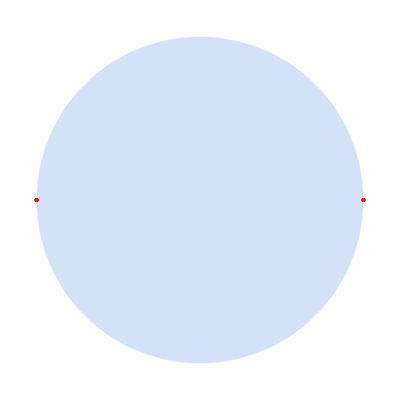

```mathematica
fig1=Show[{
Region[Style[regs⟦2⟧,Opacity[.5]]],
Region[Style[regs⟦1⟧,Red,PointSize[Large]]],
Region[Style[regs⟦3⟧,Red,PointSize[Large]]]
}]
```

Możemy również wybrać przykładowe elemnty z każdego z cylindrów.

```mathematica
pts=SemialgebraicComponentInstances[system,vars]
```

{{x_1→-1,x_2→0},{x_1→-1/2,x_2→-1/(√2)},{x_1→-1/2,x_2→1/(√2)},{x_1→0,x_2→-1},{x_1→0,x_2→0},{x_1→0,x_2→1},{x_1→0,x_2→-1/(√2)},{x_1→0,x_2→1/(√2)},{x_1→1/2,x_2→-1/(√2)},{x_1→1/2,x_2→1/(√2)},{x_1→1,x_2→0},{x_1→-1/(√2),x_2→0},{x_1→-1/(√2),x_2→-1/(√2)},{x_1→-1/(√2),x_2→1/(√2)},{x_1→1/(√2),x_2→0},{x_1→1/(√2),x_2→-1/(√2)},{x_1→1/(√2),x_2→1/(√2)}}

Warto zauważyć, żę z każdego cylindra został wybrany przynajmniej jeden elementy. A zatem, jeżeli cylindry są jednoelementowe to te elementy zostaną wybrane.

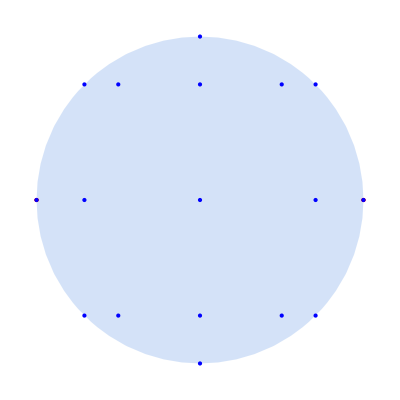

```mathematica
Show[
fig1,
Graphics[{PointSize[Medium],Blue,Point[vars/.pts]}]
]
```

Przykład. Rozważmy prosty układ algebraiczny.

```mathematica
system=x[1]^2+x[2]^2<1&&x[1]>x[2]^2
```

x_1^2+x_2^2<1&&x_1>x_2^2

```mathematica
vars=Table[x[k],{k,1,2}]
```

{x_1,x_2}

Jak wygląda jego rozwiązanie w formie cylindrycznej?

```mathematica
sol=CylindricalDecomposition[system,vars]
```

(0<x_1≤1/2 (-1+√5)&&-√x_1<x_2<√x_1)||(1/2 (-1+√5)<x_1<1&&-√(1-x_1^2)<x_2<√(1-x_1^2))

Tutaj mamy jedynie dwa cylindry.

```mathematica
{cyl1,cyl2}=List@@sol
```

{0<x_1≤1/2 (-1+√5)&&-√x_1<x_2<√x_1,1/2 (-1+√5)<x_1<1&&-√(1-x_1^2)<x_2<√(1-x_1^2)}

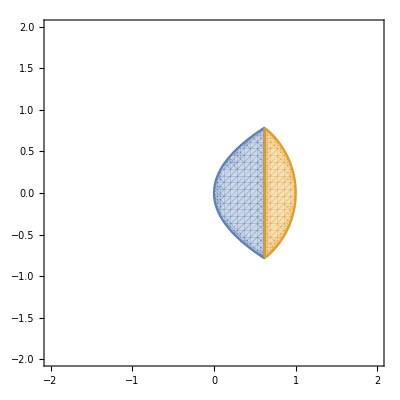

```mathematica
fig1=RegionPlot[{cyl1,cyl2},{x[1],-2,2},{x[2],-2,2},PlotPoints->50]
```

Podobnie jak poprzednio możemy wybrać elementy z każdego z cylindrów.

```mathematica
pts=SemialgebraicComponentInstances[system,vars]
```

{{x_1→5/16,x_2→0},{x_1→5/16,x_2→-(√(5/2))/4},{x_1→5/16,x_2→(√(5/2))/4},{x_1→13/16,x_2→0},{x_1→13/16,x_2→-(√(5/2))/4},{x_1→13/16,x_2→(√(5/2))/4},{x_1→1/2 (-1+√5),x_2→0},{x_1→1/2 (-1+√5),x_2→-(√5)/4},{x_1→1/2 (-1+√5),x_2→(√5)/4}}

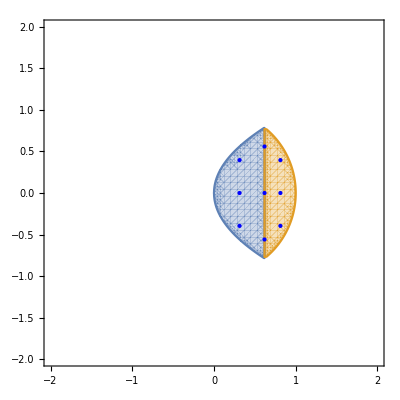

```mathematica
Show[
fig1,
Graphics[{PointSize[Medium],Blue,Point[vars/.pts]}]
]
```

Przykład. Rozważmy prosty układ algebraiczny.

```mathematica
system=x[1]^2+x[2]^2<Sqrt[x[3]]&&x[1] x[3]>x[2]^2&&x[3]<4-x[1]^2
```

x_1^2+x_2^2<√x_3&&x_1 x_3>x_2^2&&x_3<4-x_1^2

```mathematica
vars=Table[x[k],{k,1,3}]
```

{x_1,x_2,x_3}

Jak wygląda jego rozwiązanie w formie cylindrycznej?

```mathematica
sol=CylindricalDecomposition[system,vars];
```

```mathematica
Framed/@LogicalExpand[sol]
```

x_1==Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&x_2==Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,1]&&x_2^2/x_1<x_3&&x_3<4-x_1^2||x_1==Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&x_2==Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,3]&&x_2^2/x_1<x_3&&x_3<4-x_1^2||x_1==Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&Root[-4+#1^4+x_1^2+2 #1^2 x_1^2+x_1^4&,1]<x_2&&x_2<Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,1]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2||x_1==Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,1]<x_2&&x_2<Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,3]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2||x_1==Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,3]<x_2&&x_2<Root[-4+#1^4+x_1^2+2 #1^2 x_1^2+x_1^4&,2]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2||0<x_1&&Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,2]<x_2&&x_2<Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,3]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2&&x_1≤Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509||0<x_1&&-√(4 x_1-x_1^3)<x_2&&x_2^2/x_1<x_3&&x_3<4-x_1^2&&x_1≤Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509&&x_2≤Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,2]||0<x_1&&x_2<√(4 x_1-x_1^3)&&x_2^2/x_1<x_3&&x_3<4-x_1^2&&Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,3]≤x_2&&x_1≤Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509||Root[-4+#1^4+x_1^2+2 #1^2 x_1^2+x_1^4&,1]<x_2&&Root0.630Root[-1+4 #1^3&,1]0.6299605249474366<x_1&&x_1<Root1.25Root[-4+#1^2+#1^4&,2]1.2496210676876531&&x_2<Root[-4+#1^4+x_1^2+2 #1^2 x_1^2+x_1^4&,2]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2||Root[-4+#1^4+x_1^2+2 #1^2 x_1^2+x_1^4&,1]<x_2&&Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509<x_1&&x_1<Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&x_2<Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,1]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2||Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,2]<x_2&&Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509<x_1&&x_1<Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&x_2<Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,3]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2||Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,4]<x_2&&Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509<x_1&&x_1<Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&x_2<Root[-4+#1^4+x_1^2+2 #1^2 x_1^2+x_1^4&,2]&&x_1^4+2 x_1^2 x_2^2+x_2^4<x_3&&x_3<4-x_1^2||Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509<x_1&&x_1<Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&x_2^2/x_1<x_3&&x_3<4-x_1^2&&Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,1]≤x_2&&x_2≤Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,2]||Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509<x_1&&x_1<Root0.630Root[-1+4 #1^3&,1]0.6299605249474366&&x_2^2/x_1<x_3&&x_3<4-x_1^2&&Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,3]≤x_2&&x_2≤Root[#1^4 x_1+x_1^5+#1^2 (-1+2 x_1^3)&,4]

Podobnie jak poprzednio możemy stworzyć wizualizację.

```mathematica
fig1=RegionPlot3D[List@@sol,{x[1],-2,2},{x[2],-2,2},{x[3],0,5},PlotPoints->50,Mesh->None,PlotStyle->Directive[Opacity[.2]],MaxRecursion->5]
```

-Graphics3D-

Podobnie jak poprzednio możemy wybrać elementy z każdego z cylindrów.

```mathematica
pts=SemialgebraicComponentInstances[system,vars]
```

{{x_1→7/32,x_2→-1/64,x_3→2},{x_1→7/32,x_2→0,x_3→2},{x_1→7/32,x_2→1/64,x_3→2},{x_1→7/32,x_2→-(√7)/4,x_3→3},{x_1→7/32,x_2→(√7)/4,x_3→3},{x_1→7/32,x_2→-1/32 √(1/7 (16041-128 √15698)),x_3→2},{x_1→7/32,x_2→1/32 √(1/7 (16041-128 √15698)),x_3→2},{x_1→35/64,x_2→0,x_3→2},{x_1→35/64,x_2→-(√(5/2))/2,x_3→5/2},{x_1→35/64,x_2→-(√(5/2))/8,x_3→2},{x_1→35/64,x_2→(√(5/2))/8,x_3→2},{x_1→35/64,x_2→(√(5/2))/2,x_3→5/2},{x_1→35/64,x_2→-(√(11/2))/2,x_3→13/4},{x_1→35/64,x_2→(√(11/2))/2,x_3→13/4},{x_1→35/64,x_2→-1/64 √(1/35 (88197-512 √22661)),x_3→2},{x_1→35/64,x_2→1/64 √(1/35 (88197-512 √22661)),x_3→2},{x_1→35/64,x_2→-1/64 √(1/35 (88197+512 √22661)),x_3→23/8},{x_1→35/64,x_2→1/64 √(1/35 (88197+512 √22661)),x_3→23/8},{x_1→15/16,x_2→0,x_3→2},{x_1→15/16,x_2→-(√7)/4,x_3→19/8},{x_1→15/16,x_2→(√7)/4,x_3→19/8},{x_1→Root0.630Root[-1+4 #1^3&,1]0.6299605249474366,x_2→-1,x_3→11/4},{x_1→Root0.630Root[-1+4 #1^3&,1]0.6299605249474366,x_2→0,x_3→2},{x_1→Root0.630Root[-1+4 #1^3&,1]0.6299605249474366,x_2→1,x_3→11/4},{x_1→Root0.630Root[-1+4 #1^3&,1]0.6299605249474366,x_2→-(√3)/4,x_3→2},{x_1→Root0.630Root[-1+4 #1^3&,1]0.6299605249474366,x_2→(√3)/4,x_3→2},{x_1→Root0.630Root[-1+4 #1^3&,1]0.6299605249474366,x_2→-√(Root0.397Root[{-1+4 #1^3&,#1^2-2 #2+4 #1 #2^2&},{1,2}]0.3968502629920499),x_3→2},{x_1→Root0.630Root[-1+4 #1^3&,1]0.6299605249474366,x_2→√(Root0.397Root[{-1+4 #1^3&,#1^2-2 #2+4 #1 #2^2&},{1,2}]0.3968502629920499),x_3→2},{x_1→Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509,x_2→0,x_3→2},{x_1→Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509,x_2→-(√(7/2))/2,x_3→23/8},{x_1→Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509,x_2→-(√(7/2))/16,x_3→2},{x_1→Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509,x_2→(√(7/2))/16,x_3→2},{x_1→Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509,x_2→(√(7/2))/2,x_3→23/8},{x_1→Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509,x_2→-√(Root0.0254Root[{-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,#1^5-#2+2 #1^3 #2+#1 #2^2&},{4,1}]0.025391429610595425),x_3→2},{x_1→Root0.458Root[-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,4]0.4582566948655509,x_2→√(Root0.0254Root[{-4+17 #1^2+8 #1^3-7 #1^4-2 #1^5+#1^6&,#1^5-#2+2 #1^3 #2+#1 #2^2&},{4,1}]0.025391429610595425),x_3→2}}

```mathematica
Show[
fig1,
Graphics3D[{PointSize[Medium],Blue,Point[vars/.pts//N]}]
]
```

-Graphics3D-

## Algorytmy

Algorytm. Algorytm wykorzystujący powyższe podejście jako wejście będzie przyjmował grę oraz nazwę symbolu do zapisu odpowiedniego układu algebraicznego. Następnie będzie tworzył układ algebraiczny opisujący zbiór równowag Nasha. Ostatecznie będzie (wersja A) wykorzystywał algorytm CAD do stworzenia cylindrycznego opisu rozwiązania lub (B) wybierał elementy z każdego komponentu.

## Implementacje

### Reprezentacja

Implementacja. W pierwszej kolejności trzeba zaproponować ogólną implementację obliczania funkcji z.

```mathematica
ClearAll[computeZ]
computeZ[game_,profile_]:=Module[{numOfPlayer,numOfActions,playerActions,uAtProfile,uAtActions,player,temp,z={},k,j},
(* liczba graczy *)
numOfPlayer=Length[game];
(* liczba akcji dla każdego gracza *)
numOfActions=Dimensions[game["player 1"]];
(* wypłata w profilu *)
uAtProfile=getPayoff[game,profile];
(* obliczanie z *)
For[player=1,player≤numOfPlayer,player++,
temp=profile;
(* wypłat dla akcji dla danego gracza *)
playerActions=IdentityMatrix[numOfActions⟦player⟧];
uAtActions=getPayoff[game,#]⟦player⟧&/@Table[temp⟦player⟧=playerActions⟦k⟧; temp,{k,1,numOfActions⟦player⟧}];
(* przekształcania *)
z=Append[z,(uAtActions-uAtProfile⟦player⟧)];
];
z
]
```

Przykład. Zdefiniujemy dowolną grę trzy osobową.

```mathematica
g0=<|"player 1"->{{{a1,a2},{a3,a4}},{{a5,a6},{a7,a8}}},"player 2"->{{{b1,b2},{b3,b4}},{{b5,b6},{b7,b8}}},"player 3"->{{{c1,c2},{c3,c4}},{{c5,c6},{c7,c8}}}|>;
```

```mathematica
MatrixForm/@g0
```

<|player 1→((a1
a2) | (a3
a4)
(a5
a6) | (a7
a8)),player 2→((b1
b2) | (b3
b4)
(b5
b6) | (b7
b8)),player 3→((c1
c2) | (c3
c4)
(c5
c6) | (c7
c8))|>

Obliczmy przykładowe odwzorowanie z.

```mathematica
ClearAll[x]
Format[x[s_]]:=Subscript[Style[x,Blue], Style[s,Directive[Blue,Bold]]]
Format[x[s_][w_]]:=Subscript[Style[x,Blue], Style[s,Directive[Blue,Bold]],Style[w,Blue]]
```

```mathematica
z=computeZ[g0,{{x[1],1-x[1]},{x[2],1-x[2]},{x[3],1-x[3]}}]//Expand//Simplify
```

{{-(-1+x_1) (a2 x_2-a6 x_2+a4 (-1+x_2) (-1+x_3)-a8 (-1+x_2) (-1+x_3)+a3 x_3-a7 x_3+a1 x_2 x_3-a2 x_2 x_3-a3 x_2 x_3-a5 x_2 x_3+a6 x_2 x_3+a7 x_2 x_3),x_1 (-a2 x_2+a6 x_2-a4 (-1+x_2) (-1+x_3)+a8 (-1+x_2) (-1+x_3)-a3 x_3+a7 x_3-a1 x_2 x_3+a2 x_2 x_3+a3 x_2 x_3+a5 x_2 x_3-a6 x_2 x_3-a7 x_2 x_3)},{-(-1+x_2) (b2 x_1-b4 x_1+b6 (-1+x_1) (-1+x_3)-b8 (-1+x_1) (-1+x_3)+b5 x_3-b7 x_3+b1 x_1 x_3-b2 x_1 x_3-b3 x_1 x_3+b4 x_1 x_3-b5 x_1 x_3+b7 x_1 x_3),x_2 (-b2 x_1+b4 x_1-b6 (-1+x_1) (-1+x_3)+b8 (-1+x_1) (-1+x_3)-b5 x_3+b7 x_3-b1 x_1 x_3+b2 x_1 x_3+b3 x_1 x_3-b4 x_1 x_3+b5 x_1 x_3-b7 x_1 x_3)},{-(c3 x_1-c4 x_1+c7 (-1+x_1) (-1+x_2)-c8 (-1+x_1) (-1+x_2)+c5 x_2-c6 x_2+c1 x_1 x_2-c2 x_1 x_2-c3 x_1 x_2+c4 x_1 x_2-c5 x_1 x_2+c6 x_1 x_2) (-1+x_3),(-c3 x_1+c4 x_1-c7 (-1+x_1) (-1+x_2)+c8 (-1+x_1) (-1+x_2)-c5 x_2+c6 x_2-c1 x_1 x_2+c2 x_1 x_2+c3 x_1 x_2-c4 x_1 x_2+c5 x_1 x_2-c6 x_1 x_2) x_3}}

Układ nierówności jest tutaj zadany jak poniżej.

```mathematica
cond=Thread[#≤0]&/@z;
Framed/@cond
```

{{-(-1+x_1) (a2 x_2-a6 x_2+a4 (-1+x_2) (-1+x_3)-a8 (-1+x_2) (-1+x_3)+a3 x_3-a7 x_3+a1 x_2 x_3-a2 x_2 x_3-a3 x_2 x_3-a5 x_2 x_3+a6 x_2 x_3+a7 x_2 x_3)≤0,x_1 (-a2 x_2+a6 x_2-a4 (-1+x_2) (-1+x_3)+a8 (-1+x_2) (-1+x_3)-a3 x_3+a7 x_3-a1 x_2 x_3+a2 x_2 x_3+a3 x_2 x_3+a5 x_2 x_3-a6 x_2 x_3-a7 x_2 x_3)≤0},{-(-1+x_2) (b2 x_1-b4 x_1+b6 (-1+x_1) (-1+x_3)-b8 (-1+x_1) (-1+x_3)+b5 x_3-b7 x_3+b1 x_1 x_3-b2 x_1 x_3-b3 x_1 x_3+b4 x_1 x_3-b5 x_1 x_3+b7 x_1 x_3)≤0,x_2 (-b2 x_1+b4 x_1-b6 (-1+x_1) (-1+x_3)+b8 (-1+x_1) (-1+x_3)-b5 x_3+b7 x_3-b1 x_1 x_3+b2 x_1 x_3+b3 x_1 x_3-b4 x_1 x_3+b5 x_1 x_3-b7 x_1 x_3)≤0},{-(c3 x_1-c4 x_1+c7 (-1+x_1) (-1+x_2)-c8 (-1+x_1) (-1+x_2)+c5 x_2-c6 x_2+c1 x_1 x_2-c2 x_1 x_2-c3 x_1 x_2+c4 x_1 x_2-c5 x_1 x_2+c6 x_1 x_2) (-1+x_3)≤0,(-c3 x_1+c4 x_1-c7 (-1+x_1) (-1+x_2)+c8 (-1+x_1) (-1+x_2)-c5 x_2+c6 x_2-c1 x_1 x_2+c2 x_1 x_2+c3 x_1 x_2-c4 x_1 x_2+c5 x_1 x_2-c6 x_1 x_2) x_3≤0}}

Dodatkowo trzeba oczywiście dołożyć standardowe warunki związane z prawdopodobieństwem.

```mathematica
condPr=Table[0<=x[k]≤1,{k,1,3,1}]
```

{0≤x_1≤1,0≤x_2≤1,0≤x_3≤1}

Ostatecznie całość układu wygląda w następujący sposób.

```mathematica
cond=Append[cond, condPr];
Framed/@cond
```

{{-(-1+x_1) (a2 x_2-a6 x_2+a4 (-1+x_2) (-1+x_3)-a8 (-1+x_2) (-1+x_3)+a3 x_3-a7 x_3+a1 x_2 x_3-a2 x_2 x_3-a3 x_2 x_3-a5 x_2 x_3+a6 x_2 x_3+a7 x_2 x_3)≤0,x_1 (-a2 x_2+a6 x_2-a4 (-1+x_2) (-1+x_3)+a8 (-1+x_2) (-1+x_3)-a3 x_3+a7 x_3-a1 x_2 x_3+a2 x_2 x_3+a3 x_2 x_3+a5 x_2 x_3-a6 x_2 x_3-a7 x_2 x_3)≤0},{-(-1+x_2) (b2 x_1-b4 x_1+b6 (-1+x_1) (-1+x_3)-b8 (-1+x_1) (-1+x_3)+b5 x_3-b7 x_3+b1 x_1 x_3-b2 x_1 x_3-b3 x_1 x_3+b4 x_1 x_3-b5 x_1 x_3+b7 x_1 x_3)≤0,x_2 (-b2 x_1+b4 x_1-b6 (-1+x_1) (-1+x_3)+b8 (-1+x_1) (-1+x_3)-b5 x_3+b7 x_3-b1 x_1 x_3+b2 x_1 x_3+b3 x_1 x_3-b4 x_1 x_3+b5 x_1 x_3-b7 x_1 x_3)≤0},{-(c3 x_1-c4 x_1+c7 (-1+x_1) (-1+x_2)-c8 (-1+x_1) (-1+x_2)+c5 x_2-c6 x_2+c1 x_1 x_2-c2 x_1 x_2-c3 x_1 x_2+c4 x_1 x_2-c5 x_1 x_2+c6 x_1 x_2) (-1+x_3)≤0,(-c3 x_1+c4 x_1-c7 (-1+x_1) (-1+x_2)+c8 (-1+x_1) (-1+x_2)-c5 x_2+c6 x_2-c1 x_1 x_2+c2 x_1 x_2+c3 x_1 x_2-c4 x_1 x_2+c5 x_1 x_2-c6 x_1 x_2) x_3≤0},{0≤x_1≤1,0≤x_2≤1,0≤x_3≤1}}

Przykład. Zdefiniujemy trzy osobową grę koordynacyjną.

```mathematica
g1=<|"player 1"->{{{1,0},{0,0}},{{0,0},{0,1}}},"player 2"->{{{1,0},{0,0}},{{0,0},{0,1}}},"player 3"->{{{1,0},{0,0}},{{0,0},{0,1}}}|>;
MatrixForm/@g1
```

<|player 1→((1
0) | (0
0)
(0
0) | (0
1)),player 2→((1
0) | (0
0)
(0
0) | (0
1)),player 3→((1
0) | (0
0)
(0
0) | (0
1))|>

Podobnie jak poprzednio zdefiniujemy dla niej układ algebraiczny opisujący zbiór równowag Nasha.

```mathematica
z=computeZ[g1,{{x[1],1-x[1]},{x[2],1-x[2]},{x[3],1-x[3]}}]//Expand//Simplify
```

{{-(-1+x_1) (-1+x_2+x_3),-x_1 (-1+x_2+x_3)},{-(-1+x_2) (-1+x_1+x_3),-x_2 (-1+x_1+x_3)},{-(-1+x_1+x_2) (-1+x_3),-(-1+x_1+x_2) x_3}}

```mathematica
cond=Thread[#≤0]&/@z;
condPr=Table[0<=x[k]≤1,{k,1,3,1}];
cond=Append[cond,condPr];
Framed/@cond
```

{{-(-1+x_1) (-1+x_2+x_3)≤0,-x_1 (-1+x_2+x_3)≤0},{-(-1+x_2) (-1+x_1+x_3)≤0,-x_2 (-1+x_1+x_3)≤0},{-(-1+x_1+x_2) (-1+x_3)≤0,-(-1+x_1+x_2) x_3≤0},{0≤x_1≤1,0≤x_2≤1,0≤x_3≤1}}

```mathematica
system=And@@(Flatten[cond])
```

-(-1+x_1) (-1+x_2+x_3)≤0&&-x_1 (-1+x_2+x_3)≤0&&-(-1+x_2) (-1+x_1+x_3)≤0&&-x_2 (-1+x_1+x_3)≤0&&-(-1+x_1+x_2) (-1+x_3)≤0&&-(-1+x_1+x_2) x_3≤0&&0≤x_1≤1&&0≤x_2≤1&&0≤x_3≤1

```mathematica
vars=Table[x[k],{k,1,3,1}]
```

{x_1,x_2,x_3}

```mathematica
CylindricalDecomposition[system,vars]
```

(x_1==0&&x_2==0&&x_3==0)||(x_1==1/2&&x_2==1/2&&x_3==1/2)||(x_1==1&&x_2==1&&x_3==1)

Jak widać, otrzymane rozwiązanie w formie cylindrycznej poprawnie opisuje wszystkie równowagi Nasha.

Przykład. Powtórzmy powyższy przykład ale dla gry antykoordynacyjnej.

```mathematica
g2=<|"player 1"->{{{0,1},{1,1}},{{1,1},{1,0}}},"player 2"->{{{0,1},{1,1}},{{1,1},{1,0}}},"player 3"->{{{0,1},{1,1}},{{1,1},{1,0}}}|>;
MatrixForm/@g2
```

<|player 1→((0
1) | (1
1)
(1
1) | (1
0)),player 2→((0
1) | (1
1)
(1
1) | (1
0)),player 3→((0
1) | (1
1)
(1
1) | (1
0))|>

Podobnie jak poprzednio obliczamy odwzorowanie z do daje następujący wynik.

```mathematica
z=computeZ[g2,{{x[1],1-x[1]},{x[2],1-x[2]},{x[3],1-x[3]}}]//Expand//Simplify
```

{{(-1+x_1) (-1+x_2+x_3),x_1 (-1+x_2+x_3)},{(-1+x_2) (-1+x_1+x_3),x_2 (-1+x_1+x_3)},{(-1+x_1+x_2) (-1+x_3),(-1+x_1+x_2) x_3}}

Na podstawie obliczonego odwzorowania z możemy stworzyć system algebraiczny opisujący zbiór równowag Nasha.

```mathematica
cond=Thread[#≤0]&/@z;
condPr=Table[0<=x[k]≤1,{k,1,3,1}];
cond=Append[cond,condPr];
Framed/@cond
```

{{(-1+x_1) (-1+x_2+x_3)≤0,x_1 (-1+x_2+x_3)≤0},{(-1+x_2) (-1+x_1+x_3)≤0,x_2 (-1+x_1+x_3)≤0},{(-1+x_1+x_2) (-1+x_3)≤0,(-1+x_1+x_2) x_3≤0},{0≤x_1≤1,0≤x_2≤1,0≤x_3≤1}}

```mathematica
system=And@@(Flatten[cond])
```

(-1+x_1) (-1+x_2+x_3)≤0&&x_1 (-1+x_2+x_3)≤0&&(-1+x_2) (-1+x_1+x_3)≤0&&x_2 (-1+x_1+x_3)≤0&&(-1+x_1+x_2) (-1+x_3)≤0&&(-1+x_1+x_2) x_3≤0&&0≤x_1≤1&&0≤x_2≤1&&0≤x_3≤1

```mathematica
vars=Table[x[k],{k,1,3,1}]
```

{x_1,x_2,x_3}

Ostatecznie możemy znaleźć rozwiązanie w formie cylindrycznej powyższego układu algebraicznego.

```mathematica
sol=CylindricalDecomposition[system,vars]//LogicalExpand
```

(x_1==1/2&&x_2==0&&x_3==1)||(x_1==1/2&&x_2==1/2&&x_3==1/2)||(x_1==1/2&&x_2==1&&x_3==0)||(x_1==0&&x_2==1&&0≤x_3&&x_3≤1)||(x_1==0&&x_3==1&&x_2<1&&0≤x_2)||(x_1==1&&x_2==0&&0≤x_3&&x_3≤1)||(x_1==1&&x_3==0&&0<x_2&&x_2≤1)||(x_2==0&&x_3==1&&0<x_1&&x_1<1/2)||(x_2==0&&x_3==1&&1/2<x_1&&x_1<1)||(x_2==1&&x_3==0&&0<x_1&&x_1<1/2)||(x_2==1&&x_3==0&&1/2<x_1&&x_1<1)

```mathematica
Framed/@sol
```

x_1==1/2&&x_2==0&&x_3==1||x_1==1/2&&x_2==1/2&&x_3==1/2||x_1==1/2&&x_2==1&&x_3==0||x_1==0&&x_2==1&&0≤x_3&&x_3≤1||x_1==0&&x_3==1&&x_2<1&&0≤x_2||x_1==1&&x_2==0&&0≤x_3&&x_3≤1||x_1==1&&x_3==0&&0<x_2&&x_2≤1||x_2==0&&x_3==1&&0<x_1&&x_1<1/2||x_2==0&&x_3==1&&1/2<x_1&&x_1<1||x_2==1&&x_3==0&&0<x_1&&x_1<1/2||x_2==1&&x_3==0&&1/2<x_1&&x_1<1

```mathematica
Show@Table[
Region[Style[ImplicitRegion[sol⟦k⟧,vars//Evaluate],ColorData[45][k],PointSize[Large],Thickness[0.01]]],
{k,1,Length[sol]}]
```

-Graphics3D-

Uwaga. Implementacja będzie zatem polegała na tym aby na podstawie podanej gry oraz symbolu stworzyć automatycznie układ algebraiczny opisujący zbiór równowag Nasha a następnie wykorzystać algorytm CAD i zwrócić wynik w postaci rozwiniętej. Poniżej zaproponowana jest taka implementacja.

```mathematica
(* dodatkowe funkcje techniczne *)
ClearAll[createProfile]
createProfile[game_,var_]:=MapIndexed[var[(First[#2])][#1]&,Range/@Dimensions[game["player 1"]],{2}]
```

```mathematica
(* dodatkowe funkcje techniczne *)
ClearAll[simplex]
simplex[n_,var_]:=Module[{vars,k},
vars=Table[var[k],{k,1,n-1}];
ImplicitRegion[Append[(#≥0)&/@vars,Total[vars]≤1],Evaluate[vars]]
]
```

```mathematica
(* dodatkowe funkcje techniczne *)
ClearAll[region]
region[dims_,var_]:=Module[{ret,vars},
vars=Table[var[k],{k,1,Length[dims]}];
RegionProduct@@MapThread[simplex,{dims,vars}]
]
```

```mathematica
(* dodatkowe funkcje do wizualiacji *)
ClearAll[plotRegion]
plotRegion[reg_,quality_]:=Region[Style[BoundaryDiscretizeRegion[reg,{{-1,1},{-1,1},{-1,1}},MaxCellMeasure->quality],Opacity[.2]]]
```

```mathematica
(* dodatkowe funkcje do wizualizacji *)
ClearAll[plotSolution]
plotSolution[sol_]:=Module[{k,ret},
If[MemberQ[{Or}, Head[sol["solution"]]],
(* head = or *)
Return@Table[
Region[Style[ImplicitRegion[sol["solution"]⟦k⟧,sol["variables reduced"]//Evaluate],ColorData[45][k],PointSize[Large],Thickness[0.01]]],{k,1,Length[sol["solution"]]}],
(* head ≠ or *)
Return@Region[Style[
ImplicitRegion[sol["solution"],sol["variables reduced"]//Evaluate],
ColorData[45][1],PointSize[Large],Thickness[0.01]]]
];
]
```

```mathematica
ClearAll[findNashEquilibriaThroughCAD,exampleInstances,timeConstrained]
Options[findNashEquilibriaThroughCAD]={exampleInstances->False,timeConstrained->10};
findNashEquilibriaThroughCAD[game_,var_,OptionsPattern[]]:=Module[{profile,reduction,profileReduced,varsReduced,z,system,sol,reg},
(* tworzenie układu zmiennych *)
profile=createProfile[game,var];
reduction=(Last[#]->1-Total@Most[#])&/@profile;
profileReduced=profile/.reduction;
varsReduced=Flatten[Most/@profile];
reg=region[Dimensions[game["player 1"]],var];
(* tworzenie układu algebraicznego *)
z=computeZ[game,profileReduced]//Expand//Simplify;
system=Thread[#≤0]&/@z;
system=Append[system,(Total[#]≤1)&/@profileReduced];
system=Append[system,(#≥0)&/@Flatten[profileReduced]];
system=And@@(Flatten[system]);
(* rozwiązywanie i rozwijanie *)
sol=TimeConstrained[
CylindricalDecomposition[system,Flatten[profile]]//LogicalExpand,
OptionValue[timeConstrained]];
(* zwracanie *)
<|
"profile"->profile,
"reduction"->reduction,
"profile reduced"->profileReduced,
"variables reduced"->varsReduced,
"system"->system,
"region"->reg,
"solution"->sol
|>
]
```

Przykład. Korzystając z powyższej funkcji możem jeszcze raz obliczyć zdefiniowane powyżej gry. W pierwszej kolejności patrzymy na grę koordynacyjną.

```mathematica
ClearAll[x]
Format[x[s_]]:=Subscript[Style[x,Blue], Style[s,Directive[Blue,Bold]]]
Format[x[s_][w_]]:=Subscript[Style[x,Blue], Style[s,Directive[Blue,Bold]],Style[w,Blue]]
```

```mathematica
g1sol=findNashEquilibriaThroughCAD[g1,x,timeConstrained->10]
```

<|profile→{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)},{x_(3,1),x_(3,2)}},reduction→{x_(1,2)→1-x_(1,1),x_(2,2)→1-x_(2,1),x_(3,2)→1-x_(3,1)},profile reduced→{{x_(1,1),1-x_(1,1)},{x_(2,1),1-x_(2,1)},{x_(3,1),1-x_(3,1)}},variables reduced→{x_(1,1),x_(2,1),x_(3,1)},system→-(-1+x_(1,1)) (-1+x_(2,1)+x_(3,1))≤0&&-x_(1,1) (-1+x_(2,1)+x_(3,1))≤0&&-(-1+x_(2,1)) (-1+x_(1,1)+x_(3,1))≤0&&-x_(2,1) (-1+x_(1,1)+x_(3,1))≤0&&-(-1+x_(1,1)+x_(2,1)) (-1+x_(3,1))≤0&&-(-1+x_(1,1)+x_(2,1)) x_(3,1)≤0&&x_(1,1)≥0&&1-x_(1,1)≥0&&x_(2,1)≥0&&1-x_(2,1)≥0&&x_(3,1)≥0&&1-x_(3,1)≥0,region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}],ImplicitRegion[x_(3,1)≥0&&x_(3,1)≤1,{x_(3,1)}]],solution→(x_(1,1)==0&&x_(2,1)==0&&x_(3,1)==0)||(x_(1,1)==1/2&&x_(2,1)==1/2&&x_(3,1)==1/2)||(x_(1,1)==1&&x_(2,1)==1&&x_(3,1)==1)|>

```mathematica
figreg=plotRegion[g1sol["region"],10^-3];
```

```mathematica
Show[figreg,plotSolution[g1sol]]
```

-Graphics3D-

Podobnie możemy popatrzeć jeszcze raz na grę antykoordynacyjną.

```mathematica
sol=findNashEquilibriaThroughCAD[g2,x,timeConstrained->10]
```

<|profile→{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)},{x_(3,1),x_(3,2)}},reduction→{x_(1,2)→1-x_(1,1),x_(2,2)→1-x_(2,1),x_(3,2)→1-x_(3,1)},profile reduced→{{x_(1,1),1-x_(1,1)},{x_(2,1),1-x_(2,1)},{x_(3,1),1-x_(3,1)}},variables reduced→{x_(1,1),x_(2,1),x_(3,1)},system→(-1+x_(1,1)) (-1+x_(2,1)+x_(3,1))≤0&&x_(1,1) (-1+x_(2,1)+x_(3,1))≤0&&(-1+x_(2,1)) (-1+x_(1,1)+x_(3,1))≤0&&x_(2,1) (-1+x_(1,1)+x_(3,1))≤0&&(-1+x_(1,1)+x_(2,1)) (-1+x_(3,1))≤0&&(-1+x_(1,1)+x_(2,1)) x_(3,1)≤0&&x_(1,1)≥0&&1-x_(1,1)≥0&&x_(2,1)≥0&&1-x_(2,1)≥0&&x_(3,1)≥0&&1-x_(3,1)≥0,region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}],ImplicitRegion[x_(3,1)≥0&&x_(3,1)≤1,{x_(3,1)}]],solution→(x_(1,1)==1/2&&x_(2,1)==0&&x_(3,1)==1)||(x_(1,1)==1/2&&x_(2,1)==1/2&&x_(3,1)==1/2)||(x_(1,1)==1/2&&x_(2,1)==1&&x_(3,1)==0)||(x_(1,1)==0&&x_(2,1)==1&&0≤x_(3,1)&&x_(3,1)≤1)||(x_(1,1)==0&&x_(3,1)==1&&x_(2,1)<1&&0≤x_(2,1))||(x_(1,1)==1&&x_(2,1)==0&&0≤x_(3,1)&&x_(3,1)≤1)||(x_(1,1)==1&&x_(3,1)==0&&0<x_(2,1)&&x_(2,1)≤1)||(x_(2,1)==0&&x_(3,1)==1&&0<x_(1,1)&&x_(1,1)<1/2)||(x_(2,1)==0&&x_(3,1)==1&&1/2<x_(1,1)&&x_(1,1)<1)||(x_(2,1)==1&&x_(3,1)==0&&0<x_(1,1)&&x_(1,1)<1/2)||(x_(2,1)==1&&x_(3,1)==0&&1/2<x_(1,1)&&x_(1,1)<1)|>

```mathematica
figreg=plotRegion[sol["region"],10^-3];
```

```mathematica
Show[figreg,plotSolution[sol]]
```

-Graphics3D-

Przykład. Mając powyższe funkcje możemy również popatrzeć na całkowicie losowe gry.

```mathematica
g=generateRandomGame[BinomialDistribution[10,1/2],{2,2,2}];
MatrixForm/@g
```

<|player 1→((7
5) | (5
4)
(4
4) | (5
5)),player 2→((3
4) | (6
7)
(5
6) | (5
5)),player 3→((4
6) | (4
6)
(6
3) | (4
8))|>

```mathematica
sol=findNashEquilibriaThroughCAD[g,x,timeConstrained->20]
```

<|profile→{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)},{x_(3,1),x_(3,2)}},reduction→{x_(1,2)→1-x_(1,1),x_(2,2)→1-x_(2,1),x_(3,2)→1-x_(3,1)},profile reduced→{{x_(1,1),1-x_(1,1)},{x_(2,1),1-x_(2,1)},{x_(3,1),1-x_(3,1)}},variables reduced→{x_(1,1),x_(2,1),x_(3,1)},system→-(-1+x_(1,1)) (-1+x_(3,1)+x_(2,1) (2+x_(3,1)))≤0&&-x_(1,1) (-1+x_(3,1)+x_(2,1) (2+x_(3,1)))≤0&&-(-1+x_(2,1)) (1+x_(1,1) (-4+x_(3,1))-x_(3,1))≤0&&x_(2,1) (-1-x_(1,1) (-4+x_(3,1))+x_(3,1))≤0&&(4-7 x_(2,1)+x_(1,1) (-2+7 x_(2,1))) (-1+x_(3,1))≤0&&(4-7 x_(2,1)+x_(1,1) (-2+7 x_(2,1))) x_(3,1)≤0&&x_(1,1)≥0&&1-x_(1,1)≥0&&x_(2,1)≥0&&1-x_(2,1)≥0&&x_(3,1)≥0&&1-x_(3,1)≥0,region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}],ImplicitRegion[x_(3,1)≥0&&x_(3,1)≤1,{x_(3,1)}]],solution→x_(1,1)==1/4&&x_(2,1)==1/2&&x_(3,1)==0|>

```mathematica
figreg=plotRegion[sol["region"],10^-3];
```

```mathematica
Show[figreg,plotSolution[sol]]
```

-Graphics3D-

```mathematica
g=generateRandomGame[BinomialDistribution[10,1/2],{2,3}];
MatrixForm/@g
```

<|player 1→(2 | 6 | 5
3 | 6 | 4),player 2→(5 | 4 | 3
3 | 5 | 6)|>

```mathematica
sol=findNashEquilibriaThroughCAD[g,x,timeConstrained->20]
```

<|profile→{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2),x_(2,3)}},reduction→{x_(1,2)→1-x_(1,1),x_(2,3)→1-x_(2,1)-x_(2,2)},profile reduced→{{x_(1,1),1-x_(1,1)},{x_(2,1),x_(2,2),1-x_(2,1)-x_(2,2)}},variables reduced→{x_(1,1),x_(2,1),x_(2,2)},system→(-1+x_(1,1)) (-1+2 x_(2,1)+x_(2,2))≤0&&x_(1,1) (-1+2 x_(2,1)+x_(2,2))≤0&&-3+3 x_(2,1)+x_(1,1) (5-5 x_(2,1)-2 x_(2,2))+x_(2,2)≤0&&-1+3 x_(2,1)+x_(1,1) (2-5 x_(2,1)-2 x_(2,2))+x_(2,2)≤0&&(3-5 x_(1,1)) x_(2,1)+(1-2 x_(1,1)) x_(2,2)≤0&&x_(1,1)≥0&&1-x_(1,1)≥0&&x_(2,1)≥0&&x_(2,2)≥0&&1-x_(2,1)-x_(2,2)≥0,region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,1)≤1,{x_(1,1)}],ImplicitRegion[x_(2,1)≥0&&x_(2,2)≥0&&x_(2,1)+x_(2,2)≤1,{x_(2,1),x_(2,2)}]],solution→x_(2,1)==0&&x_(2,2)==1&&1/2≤x_(1,1)&&x_(1,1)≤2/3|>

```mathematica
figreg=plotRegion[sol["region"],10^-3];
```

```mathematica
Show[figreg,plotSolution[sol]]
```

-Graphics3D-

```mathematica
g=generateRandomGame[BinomialDistribution[10,1/2],{3,2}];
MatrixForm/@g
```

<|player 1→(4 | 2
2 | 5
5 | 5),player 2→(4 | 6
3 | 6
5 | 6)|>

```mathematica
sol=findNashEquilibriaThroughCAD[g,x,timeConstrained->20]
```

<|profile→{{x_(1,1),x_(1,2),x_(1,3)},{x_(2,1),x_(2,2)}},reduction→{x_(1,3)→1-x_(1,1)-x_(1,2),x_(2,2)→1-x_(2,1)},profile reduced→{{x_(1,1),x_(1,2),1-x_(1,1)-x_(1,2)},{x_(2,1),1-x_(2,1)}},variables reduced→{x_(1,1),x_(1,2),x_(2,1)},system→-3+x_(1,1) (3-2 x_(2,1))+(2+3 x_(1,2)) x_(2,1)≤0&&x_(1,1) (3-2 x_(2,1))+3 (-1+x_(1,2)) x_(2,1)≤0&&x_(1,1) (3-2 x_(2,1))+3 x_(1,2) x_(2,1)≤0&&(1+x_(1,1)+2 x_(1,2)) (-1+x_(2,1))≤0&&(1+x_(1,1)+2 x_(1,2)) x_(2,1)≤0&&x_(1,1)≥0&&x_(1,2)≥0&&1-x_(1,1)-x_(1,2)≥0&&x_(2,1)≥0&&1-x_(2,1)≥0,region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,2)≥0&&x_(1,1)+x_(1,2)≤1,{x_(1,1),x_(1,2)}],ImplicitRegion[x_(2,1)≥0&&x_(2,1)≤1,{x_(2,1)}]],solution→x_(1,1)==0&&x_(2,1)==0&&0≤x_(1,2)&&x_(1,2)≤1|>

```mathematica
figreg=plotRegion[sol["region"],10^-3];
```

```mathematica
Show[figreg,plotSolution[sol]]
```

-Graphics3D-

Możemy oczywiście próbować znajdować zbiory rónowag dla większych gier ale rozwiązywanie będzie zabierało znacznie więcej czasu.

```mathematica
g=generateRandomGame[BinomialDistribution[10,1/2],{3,3}];
MatrixForm/@g
```

<|player 1→(9 | 5 | 5
5 | 5 | 3
5 | 2 | 5),player 2→(3 | 6 | 7
4 | 9 | 6
4 | 4 | 5)|>

```mathematica
sol=findNashEquilibriaThroughCAD[g,x,timeConstrained->120]
```

<|profile→{{x_(1,1),x_(1,2),x_(1,3)},{x_(2,1),x_(2,2),x_(2,3)}},reduction→{x_(1,3)→1-x_(1,1)-x_(1,2),x_(2,3)→1-x_(2,1)-x_(2,2)},profile reduced→{{x_(1,1),x_(1,2),1-x_(1,1)-x_(1,2)},{x_(2,1),x_(2,2),1-x_(2,1)-x_(2,2)}},variables reduced→{x_(1,1),x_(1,2),x_(2,1),x_(2,2)},system→x_(1,2) (2-2 x_(2,1)-5 x_(2,2))-(-1+x_(1,1)) (4 x_(2,1)+3 x_(2,2))≤0&&-2+(2-4 x_(1,1)) x_(2,1)+x_(1,2) (2-2 x_(2,1)-5 x_(2,2))+5 x_(2,2)-3 x_(1,1) x_(2,2)≤0&&x_(1,2) (2-2 x_(2,1)-5 x_(2,2))-x_(1,1) (4 x_(2,1)+3 x_(2,2))≤0&&-1+3 x_(1,1) (-1+x_(2,1))+x_(2,1)+x_(1,2) (-1+x_(2,1)-4 x_(2,2))+x_(2,2)≤0&&-1+(1+3 x_(1,1)) x_(2,1)+x_(1,2) (4+x_(2,1)-4 x_(2,2))+x_(2,2)≤0&&(1+3 x_(1,1)+x_(1,2)) x_(2,1)+(1-4 x_(1,2)) x_(2,2)≤0&&x_(1,1)≥0&&x_(1,2)≥0&&1-x_(1,1)-x_(1,2)≥0&&x_(2,1)≥0&&x_(2,2)≥0&&1-x_(2,1)-x_(2,2)≥0,region→RegionProduct[ImplicitRegion[x_(1,1)≥0&&x_(1,2)≥0&&x_(1,1)+x_(1,2)≤1,{x_(1,1),x_(1,2)}],ImplicitRegion[x_(2,1)≥0&&x_(2,2)≥0&&x_(2,1)+x_(2,2)≤1,{x_(2,1),x_(2,2)}]],solution→(x_(1,1)==0&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==0&&x_(1,2)==1&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,1)==1/18&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==1/18&&x_(1,2)==17/18&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,1)==1/9&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==1/9&&x_(1,2)==8/9&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,1)==1/6&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==1/6&&x_(1,2)==5/6&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,1)==4/15&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==4/15&&x_(1,2)==11/15&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,1)==5/9&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==5/9&&x_(1,2)==4/9&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,1)==2/3&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==2/3&&x_(1,2)==1/3&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,1)==3/4&&x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0)||(x_(1,1)==3/4&&x_(1,2)==1/4&&x_(2,1)==0&&x_(2,2)==1)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&0<x_(1,1)&&x_(1,1)<1/18)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&1/18<x_(1,1)&&x_(1,1)<1/9)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&1/9<x_(1,1)&&x_(1,1)<1/6)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&1/6<x_(1,1)&&x_(1,1)<4/15)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&4/15<x_(1,1)&&x_(1,1)<5/9)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&5/9<x_(1,1)&&x_(1,1)<2/3)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&2/3<x_(1,1)&&x_(1,1)<3/4)||(x_(1,2)==0&&x_(2,1)==0&&x_(2,2)==0&&3/4<x_(1,1)&&x_(1,1)≤1)||(x_(1,2)==1-x_(1,1)&&x_(2,1)==(-3+3 x_(1,1)+15 x_(1,2)-12 x_(1,1) x_(1,2)-12 x_(1,2)^2)/(-3-16 x_(1,1)+9 x_(1,1)^2-10 x_(1,2)+34 x_(1,1) x_(1,2)+13 x_(1,2)^2)&&x_(2,2)==1-x_(2,1)&&0<x_(1,1)&&x_(1,1)<1/18)||(x_(1,2)==1-x_(1,1)&&x_(2,1)==(-3+3 x_(1,1)+15 x_(1,2)-12 x_(1,1) x_(1,2)-12 x_(1,2)^2)/(-3-16 x_(1,1)+9 x_(1,1)^2-10 x_(1,2)+34 x_(1,1) x_(1,2)+13 x_(1,2)^2)&&x_(2,2)==1-x_(2,1)&&1/18<x_(1,1)&&x_(1,1)<1/9)||(x_(1,2)==1-x_(1,1)&&x_(2,1)==(-3+3 x_(1,1)+15 x_(1,2)-12 x_(1,1) x_(1,2)-12 x_(1,2)^2)/(-3-16 x_(1,1)+9 x_(1,1)^2-10 x_(1,2)+34 x_(1,1) x_(1,2)+13 x_(1,2)^2)&&x_(2,2)==1-x_(2,1)&&1/9<x_(1,1)&&x_(1,1)<1/6)||(x_(1,2)==1-x_(1,1)&&x_(2,1)==(-3+3 x_(1,1)+15 x_(1,2)-12 x_(1,1) x_(1,2)-12 x_(1,2)^2)/(-3-16 x_(1,1)+9 x_(1,1)^2-10 x_(1,2)+34 x_(1,1) x_(1,2)+13 x_(1,2)^2)&&x_(2,2)==1-x_(2,1)&&1/6<x_(1,1)&&x_(1,1)<4/15)||(x_(1,2)==1-x_(1,1)&&x_(2,1)==(-3+3 x_(1,1)+15 x_(1,2)-12 x_(1,1) x_(1,2)-12 x_(1,2)^2)/(-3-16 x_(1,1)+9 x_(1,1)^2-10 x_(1,2)+34 x_(1,1) x_(1,2)+13 x_(1,2)^2)&&x_(2,2)==1-x_(2,1)&&4/15<x_(1,1)&&x_(1,1)<5/9)||(x_(1,2)==1-x_(1,1)&&x_(2,1)==(-3+3 x_(1,1)+15 x_(1,2)-12 x_(1,1) x_(1,2)-12 x_(1,2)^2)/(-3-16 x_(1,1)+9 x_(1,1)^2-10 x_(1,2)+34 x_(1,1) x_(1,2)+13 x_(1,2)^2)&&x_(2,2)==1-x_(2,1)&&5/9<x_(1,1)&&x_(1,1)<2/3)||(x_(1,2)==1-x_(1,1)&&x_(2,1)==(-3+3 x_(1,1)+15 x_(1,2)-12 x_(1,1) x_(1,2)-12 x_(1,2)^2)/(-3-16 x_(1,1)+9 x_(1,1)^2-10 x_(1,2)+34 x_(1,1) x_(1,2)+13 x_(1,2)^2)&&x_(2,2)==1-x_(2,1)&&2/3<x_(1,1)&&x_(1,1)<3/4)|>